```mathematica
(*  QUESTION 1 - 10 points  *)

(*Generating Lagrange Basis function based on lecture notes*)
GenerateLagrangeBasis[xPoints_] := 
Module[{m, basisPolynomials},
  m = Length[xPoints]; (* Number of points *)
  basisPolynomials = Table[Simplify[Product[If[j != i, (x - xPoints[[j]]) / (xPoints[[i]] - xPoints[[j]]), 1], {j, 1, m}]], {i, 1, m}];
  basisPolynomials
]

(* Example usage *)
xPoints = {-1, 0, 1}
lagrangeBasis = GenerateLagrangeBasis[xPoints];

(* Output all the basis polynomials *)
lagrangeBasis
```

{-1,0,1}

{1/2 (-1+x) x,1-x^2,1/2 x (1+x)}

```mathematica
(* QUESTION 2a - 10 points *)

(*Arbitrarily setting m=10, as was suggested in Assignment outline, and then creating x_k array (also from outline)*)
m = 10;
xPoints = Table[Cos[(Pi/m) * (k - (1/2))], {k, 1, m}];

(*Converting to numerical results to greatly improve computational speed*)
basisPolynomials = N[GenerateLagrangeBasis[xPoints]];

(* Compute first and second derivatives *)
firstDerivatives = Simplify[D[#, x] & /@ basisPolynomials];
secondDerivatives = Simplify[D[#, x] & /@ firstDerivatives];

(* Format table with k values and wrapped polynomial expressions *)
formattedOutput = Prepend[
   Table[
      {
         k,  (* k value *)
         Column[{basisPolynomials[[k]]}],  (* Basis polynomial *)
         Column[{firstDerivatives[[k]]}],  (* First derivative *)
         Column[{secondDerivatives[[k]]}]  (* Second derivative *)
      },
      {k, Length[xPoints]}
   ],
   {Style["k", Bold, 14], Style[Subscript[ℓ, "k"][x], Bold, 14], Style[Subscript[ℓ, "k"]'[x], Bold, 14], Style[Subscript[ℓ, "k"]''[x], Bold, 14]} (* Headers *)
];

Print["Lagrange Basis Polynomials and Their Derivatives: (m = 10)"];
Print[Grid[formattedOutput, Frame -> All]];
```

Lagrange Basis Polynomials and Their Derivatives: (m = 10)

k | ℓ_k[x] | ℓ_k'[x] | ℓ_k''[x]
1 | 2.00236 (1.41421-2. x) (0.156434-1. x) (0.45399-1. x) (0.891007-1. x) (0.156434+x) (0.45399+x) (0.891007+x) (0.987688+x) (1.41421+2. x) | 0.0160359-1.55137 x-2.35607 x^2+22.1609 x^3+28.0465 x^4-72.3591 x^5-85.4712 x^6+63.2867 x^7+72.085 x^8 | -1.55137-4.71213 x+66.4828 x^2+112.186 x^3-361.795 x^4-512.827 x^5+443.007 x^6+576.68 x^7
2 | 5.81108 (1.41421-2. x) (-0.987688+x) (-0.45399+x) (-0.156434+x) (0.156434+x) (0.45399+x) (0.891007+x) (0.987688+x) (1.41421+2. x) | -0.0571854+4.96689 x+8.36171 x^2-69.0113 x^3-96.8165 x^4+212.009 x^5+277.601 x^6-165.687 x^7-209.199 x^8 | 4.96689+16.7234 x-207.034 x^2-387.266 x^3+1060.05 x^4+1665.61 x^5-1159.81 x^6-1673.59 x^7
3 | 36.2039 (-0.987688+x) (-0.891007+x) (-0.45399+x) (-0.156434+x) (0.156434+x) (0.45399+x) (0.707107+x) (0.891007+x) (0.987688+x) | 0.141421-9.6 x-20.3647 x^2+121.6 x^3+214.96 x^4-307.2 x^5-506.854 x^6+204.8 x^7+325.835 x^8 | -9.6-40.7294 x+364.8 x^2+859.842 x^3-1536. x^4-3041.12 x^5+1433.6 x^6+2606.68 x^7
4 | -11.4049 (1.41421-2. x) (0.156434-1. x) (0.891007-1. x) (0.987688-1. x) (0.156434+x) (0.45399+x) (0.891007+x) (0.987688+x) (1.41421+2. x) | -0.432302+17.7217 x+58.5529 x^2-142.052 x^3-391.122 x^4+285.051 x^5+732.524 x^6-165.687 x^7-410.576 x^8 | 17.7217+117.106 x-426.157 x^2-1564.49 x^3+1425.25 x^4+4395.15 x^5-1159.81 x^6-3284.61 x^7
5 | 12.6424 (1.41421-2. x) (0.45399-1. x) (0.891007-1. x) (0.987688-1. x) (0.156434+x) (0.45399+x) (0.891007+x) (0.987688+x) (1.41421+2. x) | 4.03604-11.5372 x-110.626 x^2+67.3028 x^3+537.788 x^4-117.501 x^5-876.306 x^6+63.2867 x^7+455.127 x^8 | -11.5372-221.252 x+201.909 x^2+2151.15 x^3-587.505 x^4-5257.84 x^5+443.007 x^6+3641.01 x^7
6 | 1.97771 (1.41421-2. x) (-0.987688+x) (-0.891007+x) (-0.45399+x) (0.45399+x) (0.891007+x) (0.987688+x) (1.41421+2. x) (-1.+6.39245 x) | -4.03604-11.5372 x+110.626 x^2+67.3028 x^3-537.788 x^4-117.501 x^5+876.306 x^6+63.2867 x^7-455.127 x^8 | -11.5372+221.252 x+201.909 x^2-2151.15 x^3-587.505 x^4+5257.84 x^5+443.007 x^6-3641.01 x^7
7 | -5.17771 (1.41421-2. x) (-0.987688+x) (-0.891007+x) (-0.156434+x) (0.156434+x) (0.891007+x) (0.987688+x) (1.41421+2. x) (-1.+2.20269 x) | 0.432302+17.7217 x-58.5529 x^2-142.052 x^3+391.122 x^4+285.051 x^5-732.524 x^6-165.687 x^7+410.576 x^8 | 17.7217-117.106 x-426.157 x^2+1564.49 x^3+1425.25 x^4-4395.15 x^5-1159.81 x^6+3284.61 x^7
8 | 18.1019 (1.41421-2. x) (0.156434-1. x) (0.45399-1. x) (0.891007-1. x) (0.987688-1. x) (0.156434+x) (0.45399+x) (0.891007+x) (0.987688+x) | -0.141421-9.6 x+20.3647 x^2+121.6 x^3-214.96 x^4-307.2 x^5+506.854 x^6+204.8 x^7-325.835 x^8 | -9.6+40.7294 x+364.8 x^2-859.842 x^3-1536. x^4+3041.12 x^5+1433.6 x^6-2606.68 x^7
9 | -5.81108 (1.41421-2. x) (-0.987688+x) (-0.891007+x) (-0.45399+x) (-0.156434+x) (0.156434+x) (0.45399+x) (0.987688+x) (1.41421+2. x) | 0.0571854+4.96689 x-8.36171 x^2-69.0113 x^3+96.8165 x^4+212.009 x^5-277.601 x^6-165.687 x^7+209.199 x^8 | 4.96689-16.7234 x-207.034 x^2+387.266 x^3+1060.05 x^4-1665.61 x^5-1159.81 x^6+1673.59 x^7
10 | 2.00236 (1.41421-2. x) (0.156434-1. x) (0.45399-1. x) (0.891007-1. x) (0.987688-1. x) (0.156434+x) (0.45399+x) (0.891007+x) (1.41421+2. x) | -0.0160359-1.55137 x+2.35607 x^2+22.1609 x^3-28.0465 x^4-72.3591 x^5+85.4712 x^6+63.2867 x^7-72.085 x^8 | -1.55137+4.71213 x+66.4828 x^2-112.186 x^3-361.795 x^4+512.827 x^5+443.007 x^6-576.68 x^7

```mathematica
(*Question 2b - 10 points*)

(*Evaluate stencil coefficients at x=0*)
stencil1=N[Table[firstDerivatives[[k]]/. x->0,{k,1,m}]];
stencil2=N[Table[secondDerivatives[[k]]/. x->0,{k,1,m}]];

(*Evaluate stencil coefficients at boundary x=1*)
stencilBoundary1=N[Table[firstDerivatives[[k]]/. x->1 ,{k,1,m}]];
stencilBoundary2=N[Table[secondDerivatives[[k]]/. x->1,{k,1,m}]];

(*Express finite difference formulas explicitly*)
fDerivative1[x_]:=Sum[firstDerivatives[[k]]*f[xPoints[[k]]],{k,1,m}];
fDerivative2[x_]:=Sum[secondDerivatives[[k]]*f[xPoints[[k]]],{k,1,m}];

(*Display formulas at x=0 and x=1*)
fd1Center=N[fDerivative1[0]];
fd2Center=N[fDerivative2[0]];
fd1Boundary=N[fDerivative1[1]];
fd2Boundary=N[fDerivative2[1]];

Print["Explicit finite-difference approximation of first derivative at x=0: \n\n",fd1Center];
Print["\nExplicit finite-difference approximation of second derivative at x=0: \n\n",fd2Center];
Print["\nExplicit finite-difference approximation of first derivative at x=1: \n\n",fd1Boundary];
Print["\nExplicit finite-difference approximation of second derivative at x=1: \n\n",fd2Boundary];

(*Print stencil coefficient results*)
Print["\nFinite-Difference Stencil Coefficients:\n"];

Grid[Prepend[Transpose[{Range[m],stencil1,stencilBoundary1,stencil2,stencilBoundary2}],{Style["k",Bold,14],Style["L_k'(0)",Bold,14],
Style["L_k'(1)",Bold,14],Style["L_k''(0)",Bold,14],Style["L_k''(1)",Bold,14]}],Frame->All]
```

Explicit finite-difference approximation of first derivative at x=0: 

(-0.0160359-1.55137 x+2.35607 x^2+22.1609 x^3-28.0465 x^4-72.3591 x^5+85.4712 x^6+63.2867 x^7-72.085 x^8) f[-0.987688]+(0.0571854+4.96689 x-8.36171 x^2-69.0113 x^3+96.8165 x^4+212.009 x^5-277.601 x^6-165.687 x^7+209.199 x^8) f[-0.891007]+(-0.141421-9.6 x+20.3647 x^2+121.6 x^3-214.96 x^4-307.2 x^5+506.854 x^6+204.8 x^7-325.835 x^8) f[-0.707107]+(0.432302+17.7217 x-58.5529 x^2-142.052 x^3+391.122 x^4+285.051 x^5-732.524 x^6-165.687 x^7+410.576 x^8) f[-0.45399]+(-4.03604-11.5372 x+110.626 x^2+67.3028 x^3-537.788 x^4-117.501 x^5+876.306 x^6+63.2867 x^7-455.127 x^8) f[-0.156434]+(4.03604-11.5372 x-110.626 x^2+67.3028 x^3+537.788 x^4-117.501 x^5-876.306 x^6+63.2867 x^7+455.127 x^8) f[0.156434]+(-0.432302+17.7217 x+58.5529 x^2-142.052 x^3-391.122 x^4+285.051 x^5+732.524 x^6-165.687 x^7-410.576 x^8) f[0.45399]+(0.141421-9.6 x-20.3647 x^2+121.6 x^3+214.96 x^4-307.2 x^5-506.854 x^6+204.8 x^7+325.835 x^8) f[0.707107]+(-0.0571854+4.96689 x+8.36171 x^2-69.0113 x^3-96.8165 x^4+212.009 x^5+277.601 x^6-165.687 x^7-209.199 x^8) f[0.891007]+(0.0160359-1.55137 x-2.35607 x^2+22.1609 x^3+28.0465 x^4-72.3591 x^5-85.4712 x^6+63.2867 x^7+72.085 x^8) f[0.987688]

Explicit finite-difference approximation of second derivative at x=0: 

(-1.55137+4.71213 x+66.4828 x^2-112.186 x^3-361.795 x^4+512.827 x^5+443.007 x^6-576.68 x^7) f[-0.987688]+(4.96689-16.7234 x-207.034 x^2+387.266 x^3+1060.05 x^4-1665.61 x^5-1159.81 x^6+1673.59 x^7) f[-0.891007]+(-9.6+40.7294 x+364.8 x^2-859.842 x^3-1536. x^4+3041.12 x^5+1433.6 x^6-2606.68 x^7) f[-0.707107]+(17.7217-117.106 x-426.157 x^2+1564.49 x^3+1425.25 x^4-4395.15 x^5-1159.81 x^6+3284.61 x^7) f[-0.45399]+(-11.5372+221.252 x+201.909 x^2-2151.15 x^3-587.505 x^4+5257.84 x^5+443.007 x^6-3641.01 x^7) f[-0.156434]+(-11.5372-221.252 x+201.909 x^2+2151.15 x^3-587.505 x^4-5257.84 x^5+443.007 x^6+3641.01 x^7) f[0.156434]+(17.7217+117.106 x-426.157 x^2-1564.49 x^3+1425.25 x^4+4395.15 x^5-1159.81 x^6-3284.61 x^7) f[0.45399]+(-9.6-40.7294 x+364.8 x^2+859.842 x^3-1536. x^4-3041.12 x^5+1433.6 x^6+2606.68 x^7) f[0.707107]+(4.96689+16.7234 x-207.034 x^2-387.266 x^3+1060.05 x^4+1665.61 x^5-1159.81 x^6-1673.59 x^7) f[0.891007]+(-1.55137-4.71213 x+66.4828 x^2+112.186 x^3-361.795 x^4-512.827 x^5+443.007 x^6+576.68 x^7) f[0.987688]

Explicit finite-difference approximation of first derivative at x=1: 

(-0.0160359-1.55137 x+2.35607 x^2+22.1609 x^3-28.0465 x^4-72.3591 x^5+85.4712 x^6+63.2867 x^7-72.085 x^8) f[-0.987688]+(0.0571854+4.96689 x-8.36171 x^2-69.0113 x^3+96.8165 x^4+212.009 x^5-277.601 x^6-165.687 x^7+209.199 x^8) f[-0.891007]+(-0.141421-9.6 x+20.3647 x^2+121.6 x^3-214.96 x^4-307.2 x^5+506.854 x^6+204.8 x^7-325.835 x^8) f[-0.707107]+(0.432302+17.7217 x-58.5529 x^2-142.052 x^3+391.122 x^4+285.051 x^5-732.524 x^6-165.687 x^7+410.576 x^8) f[-0.45399]+(-4.03604-11.5372 x+110.626 x^2+67.3028 x^3-537.788 x^4-117.501 x^5+876.306 x^6+63.2867 x^7-455.127 x^8) f[-0.156434]+(4.03604-11.5372 x-110.626 x^2+67.3028 x^3+537.788 x^4-117.501 x^5-876.306 x^6+63.2867 x^7+455.127 x^8) f[0.156434]+(-0.432302+17.7217 x+58.5529 x^2-142.052 x^3-391.122 x^4+285.051 x^5+732.524 x^6-165.687 x^7-410.576 x^8) f[0.45399]+(0.141421-9.6 x-20.3647 x^2+121.6 x^3+214.96 x^4-307.2 x^5-506.854 x^6+204.8 x^7+325.835 x^8) f[0.707107]+(-0.0571854+4.96689 x+8.36171 x^2-69.0113 x^3-96.8165 x^4+212.009 x^5+277.601 x^6-165.687 x^7-209.199 x^8) f[0.891007]+(0.0160359-1.55137 x-2.35607 x^2+22.1609 x^3+28.0465 x^4-72.3591 x^5-85.4712 x^6+63.2867 x^7+72.085 x^8) f[0.987688]

Explicit finite-difference approximation of second derivative at x=1: 

(-1.55137+4.71213 x+66.4828 x^2-112.186 x^3-361.795 x^4+512.827 x^5+443.007 x^6-576.68 x^7) f[-0.987688]+(4.96689-16.7234 x-207.034 x^2+387.266 x^3+1060.05 x^4-1665.61 x^5-1159.81 x^6+1673.59 x^7) f[-0.891007]+(-9.6+40.7294 x+364.8 x^2-859.842 x^3-1536. x^4+3041.12 x^5+1433.6 x^6-2606.68 x^7) f[-0.707107]+(17.7217-117.106 x-426.157 x^2+1564.49 x^3+1425.25 x^4-4395.15 x^5-1159.81 x^6+3284.61 x^7) f[-0.45399]+(-11.5372+221.252 x+201.909 x^2-2151.15 x^3-587.505 x^4+5257.84 x^5+443.007 x^6-3641.01 x^7) f[-0.156434]+(-11.5372-221.252 x+201.909 x^2+2151.15 x^3-587.505 x^4-5257.84 x^5+443.007 x^6+3641.01 x^7) f[0.156434]+(17.7217+117.106 x-426.157 x^2-1564.49 x^3+1425.25 x^4+4395.15 x^5-1159.81 x^6-3284.61 x^7) f[0.45399]+(-9.6-40.7294 x+364.8 x^2+859.842 x^3-1536. x^4-3041.12 x^5+1433.6 x^6+2606.68 x^7) f[0.707107]+(4.96689+16.7234 x-207.034 x^2-387.266 x^3+1060.05 x^4+1665.61 x^5-1159.81 x^6-1673.59 x^7) f[0.891007]+(-1.55137-4.71213 x+66.4828 x^2+112.186 x^3-361.795 x^4-512.827 x^5+443.007 x^6+576.68 x^7) f[0.987688]

Finite-Difference Stencil Coefficients:

k | L_k'(0) | L_k'(1) | L_k''(0) | L_k''(1)
1 | 0.0160359 | 23.8574 | -1.55137 | 317.469
2 | -0.0571854 | -37.8314 | 4.96689 | -680.353
3 | 0.141421 | 23.3179 | -9.6 | 637.466
4 | -0.432302 | -16.0196 | 17.7217 | -479.832
5 | 4.03604 | 11.5697 | -11.5372 | 358.95
6 | -4.03604 | -8.46695 | -11.5372 | -267.203
7 | 0.432302 | 6.08586 | 17.7217 | 193.853
8 | -0.141421 | -4.11787 | -9.6 | -131.866
9 | 0.0571854 | 2.38809 | 4.96689 | 76.7003
10 | -0.0160359 | -0.783058 | -1.55137 | -25.1837

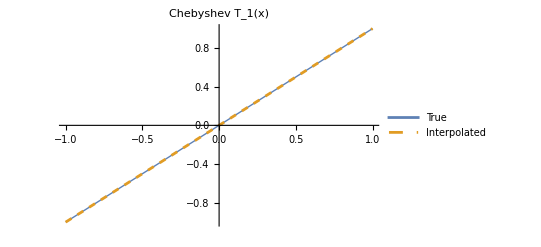
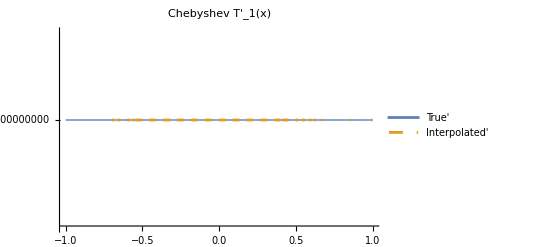
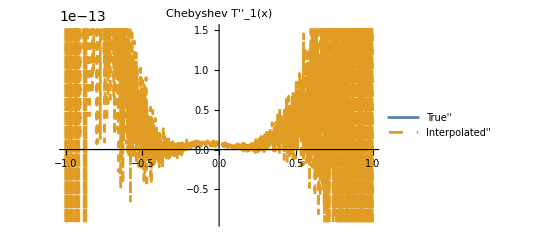
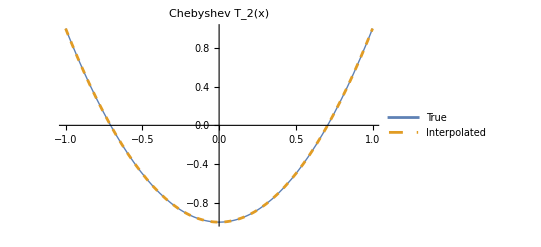
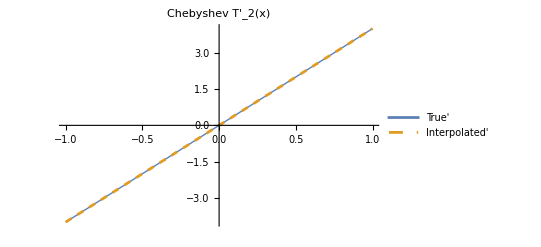
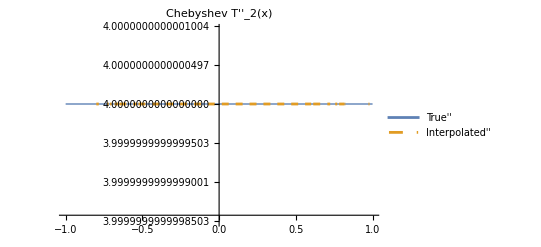
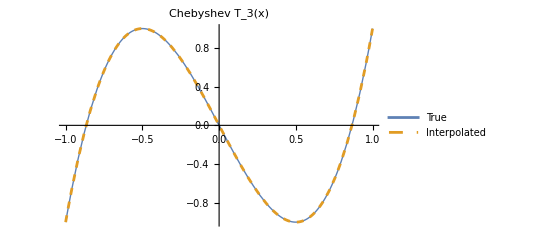
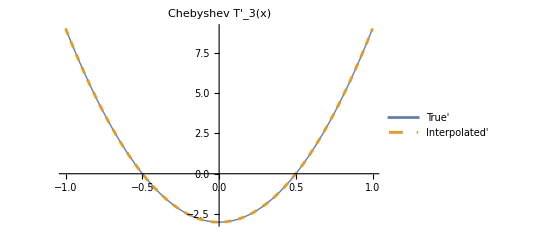
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Question 2c - 15 points*)

(*Defining Chebyshev polynomial functions for T(x), T'(x), and T''(x)*)
T[n_, x_] := ChebyshevT[n, x];
TPrime[n_, x_] := Module[{t}, D[ChebyshevT[n, t], t] /. t -> x];
TSecondPrime[n_, x_] := Module[{t}, D[ChebyshevT[n, t], {t, 2}] /. t -> x];

(* Precompute values at Chebyshev nodes. Same x_k as from Question 2a.*)
xPoints = Table[Cos[(Pi/m) * (k - (1/2))], {k, 1, m}];
SampleTn = Table[T[n, x], {x, xPoints}, {n, 1, m}];

(* Interpolants using precomputed basis polynomials from Question 2a.*)
InterpolatedTn[n_, x_] := Sum[SampleTn[[k, n]] * basisPolynomials[[k]], {k, 1, m}];
InterpolatedTnPrime[n_, x_] := Sum[SampleTn[[k, n]] * firstDerivatives[[k]], {k, 1, m}];
InterpolatedTnSecondPrime[n_, x_] := Sum[SampleTn[[k,n]] * secondDerivatives[[k]], {k, 1, m}];

(* Visualization functions *)
PlotComparison[n_] := Plot[
  {T[n, x], InterpolatedTn[n, x]}, {x, -1, 1},
  PlotStyle -> {Thick, Dashed},
  PlotLegends -> Placed[{"True", "Interpolated"}, Top],
  PlotLabel -> Row[{"Chebyshev T_", n, "(x)"}],
  Exclusions -> None
];

PlotComparisonDerivatives[n_] := Plot[
  {TPrime[n, x], InterpolatedTnPrime[n, x]}, {x, -1, 1},
  PlotStyle -> {Thick, Dashed},
  PlotLegends -> Placed[{"True'", "Interpolated'"}, Top],
  PlotLabel -> Row[{"Chebyshev T'_", n, "(x)"}],
  Exclusions -> None
];

PlotComparisonSecondDerivatives[n_] := Plot[
  {TSecondPrime[n, x], InterpolatedTnSecondPrime[n, x]}, {x, -1, 1},
  PlotStyle -> {Thick, Dashed},
  PlotLegends -> Placed[{"True''", "Interpolated''"}, Top],
  PlotLabel -> Row[{"Chebyshev T''_", n, "(x)"}],
  Exclusions -> None
];

(* Generate plots *)
Grid[Table[{PlotComparison[n], PlotComparisonDerivatives[n], PlotComparisonSecondDerivatives[n]}, {n, 1, m}],Frame -> All]
```

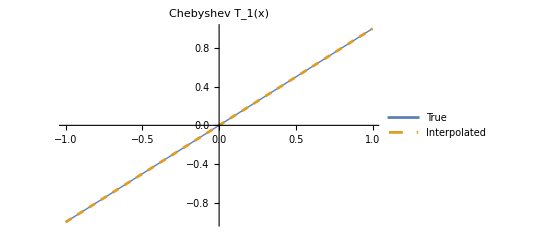
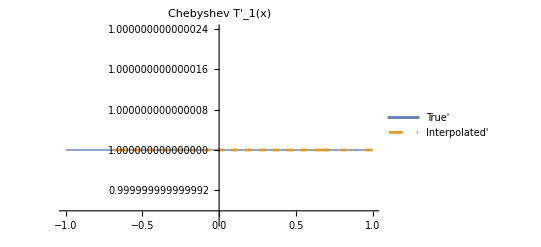
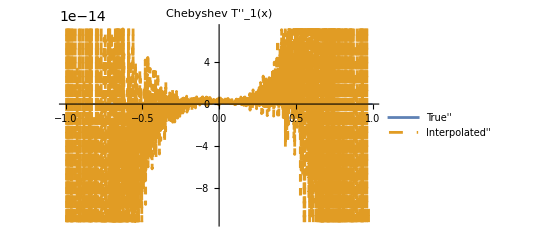
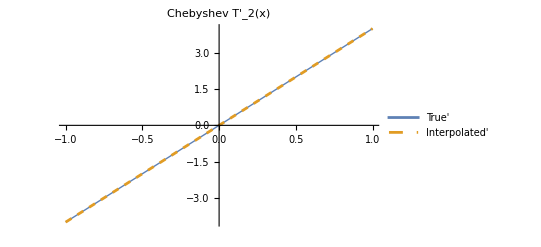
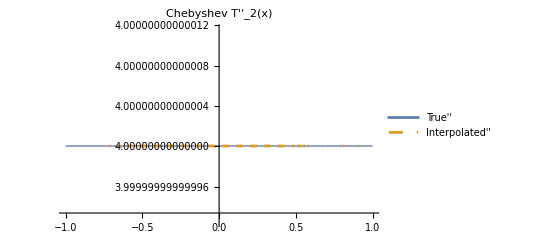
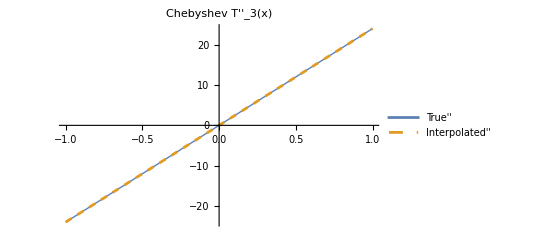
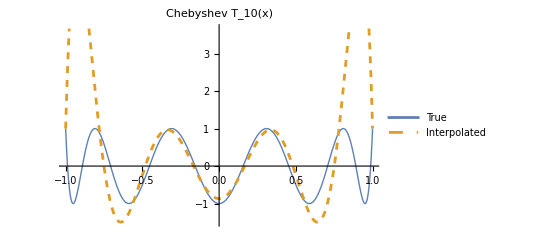
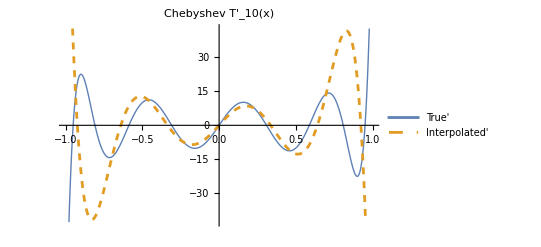
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Question 2d - 15 points*)

(* Evenly spaced grid between -1 and 1 *)
xPoints := Subdivide[-1, 1, 10 - 1];

(*Converting to numerical results to greatly improve computational speed*)
basisPolynomials = N[GenerateLagrangeBasis[xPoints]];

(* Compute first and second derivatives *)
firstDerivatives = Simplify[D[#, x] & /@ basisPolynomials];
secondDerivatives = Simplify[D[#, x] & /@ firstDerivatives];

(* Creating new SampleTn using new xPoints grid (evenly spaced vs uneven spacing like in Question 2c)*)
SampleTn = Table[T[n, x], {x, xPoints}, {n, 1, m}]; (* Dimensions: {x, n} *)

(* Interpolants using precomputed basis from Question 2a.*)
InterpolatedTn[n_, x_] := Sum[SampleTn[[k, n]] * basisPolynomials[[k]], {k, 1, m}];
InterpolatedTnPrime[n_, x_] := Sum[SampleTn[[k, n]] * firstDerivatives[[k]], {k, 1, m}];
InterpolatedTnSecondPrime[n_, x_] := Sum[SampleTn[[k,n]] * secondDerivatives[[k]], {k, 1, m}];

(* Generate plots *)
Grid[Table[{PlotComparison[n], PlotComparisonDerivatives[n], PlotComparisonSecondDerivatives[n]}, {n, 1, m}],Frame -> All]
```

```mathematica
(*Question 3c - finding derivative of interpolation function*)
p[x_]:=Simplify[Sum[(w[j] a[j])/(x-x[j]),{j,i,m}]/Sum[w[j]/(x-x[j]),{j,i,m}]];

(*Print the original interpolation formula*)
Print["Barycentric Interpolation Formula (Equation 1.36):\tf(x) = ",p[x]];

(*Define numerator N(x) and denominator D(x)*)
Nx=Sum[(w[j] a[j])/(x-x[j]),{j,i,m}];
Dx=Sum[w[j]/(x-x[j]),{j,i,m}];

Print["\n\nIf we define the numerater as Nx = ", Nx, " and the denominator as Dx = ", Dx]
Print["\n\nThen we can use the quotient rule to find f'(x)!"]

(*Compute derivatives of N(x) and D(x)*)
dNx=D[Nx,x];
dDx=D[Dx,x];

Print["\n\nThe derivative of the numerator is: dNx = ", dNx]
Print["\n\nThe derivative of the denominator is: dDx = ", dDx]

(*Apply quotient rule*)
pPrime=(dNx*Dx-Nx*dDx)/Dx^2;

(*Substitute p(x)=N(x)/D(x) into the expression*)
pPrime=pPrime/. {Nx->p*Dx};

(*Final simplified derivative formula*)
pPrime=Sum[(w[j] (p-f[j]))/(x-xj[j])^2,{j,i,m}]/Dx;

(*Print the final derivative formula*)
Print["\nDerivative of Barycentric Interpolation Formula (after quotient rule):\t",pPrime];
```

Barycentric Interpolation Formula (Equation 1.36):	f(x) = (∑_(j=i)^10 (a[j] w[j])/(x-x[j]))/(∑_(j=i)^10 w[j]/(x-x[j]))

If we define the numerater as Nx = ∑_(j=i)^10 (a[j] w[j])/(x-x[j]) and the denominator as Dx = ∑_(j=i)^10 w[j]/(x-x[j])

Then we can use the quotient rule to find f'(x)!

The derivative of the numerator is: dNx = ∑_(j=i)^10 -(a[j] w[j])/(x-x[j])^2

The derivative of the denominator is: dDx = ∑_(j=i)^10 -w[j]/(x-x[j])^2

Derivative of Barycentric Interpolation Formula (after quotient rule):	(∑_(j=i)^10 ((p-f[j]) w[j])/(x-xj[j])^2)/(∑_(j=i)^10 w[j]/(x-x[j]))